## Defining the difference equations:

```mathematica
(* Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;  Q = 0.9; (* (f Q) = a - number of human bites, per mosquito, per day *)
p = 0.9; (* surviving mosquitoes *)
EIP = 11; (* days until sporozoite matures *)
γ = 1/200. ; (* rate of end of infectious period *)
λ = 50; (* rate of mosquito emergence *)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt];
M  =450;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; (* susceptible individuals *)
```

```mathematica
(* Following the steps seen in simMacro - MACRO-Tile-Simulation *)
q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added - oneDay_popDynamics, oneDay_addCohort*)
Mt = p*(M +λ);
(* Step 2a: update mosquito infected/infectious counts - MOSQUITO-MosquitoRM-Simulation *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
(* Step 2b: mosquitoes become infectious as the sporozoite matures - MOSQUITO-MosquitoRM-Simulation *)
Zt = p*Z + Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans - simHumans - HUMAN-HumanPop-Class *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

### Comparing to an algorithm that much more closely follows MACRO-Emerge-RM

```mathematica
(* This one is meant to mirror more closely what's going on in the actual code, and so we can see more explicitly when and where everything is calculated, and in what order *)
```

```mathematica
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt];
M  =450;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; (* susceptible individuals *) 
κ = c*ii/nhuman;
EIR = f*Q*Z/nhuman;
```

```mathematica
q2 = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added - oneDay_popDynamics, oneDay_addCohort*)
M = M + λ;
(* Step 2: update mosquito infected/infectious counts - MOSQUITO-MosquitoRM-Simulation*)
M = p*M;
Y = p*Y;
Z = p*Z;
y0 = f*Q*κ*(M-Y);
Y = Y + y0;
Z = Z + Subscript[ZZ, 1];
(* Update ZZ state variables - MOSQUITO-MosquitoRM-Simulation *)
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP *y0;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
(* Step 3: update humans *)
ii= ii - γ * ii + (1-Exp[-b*EIR])(nhuman - ii);
(*Step 4: update kappa - updateKappa_PfSI - MACRO-Human-Kappa *)
κ = c*ii/nhuman;
(*Step 5: update EIR - updateEIR - MACRO-Human-Kappa*)
EIR = f*Q*Z/nhuman;
{M, Y, Z, ii},
{i,1,tsteps}];
```

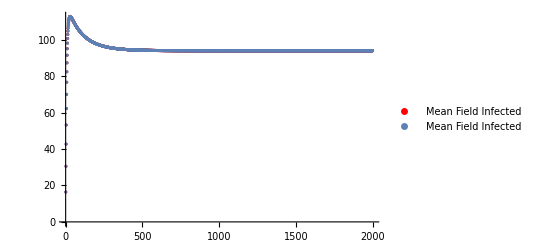

```mathematica
Show[ListPlot[q2[[;;,2]],PlotRange->Full,PlotLegends->{"Mean Field Infected"},PlotStyle->Red],ListPlot[q[[;;,2]],PlotRange->Full,PlotLegends->{"Mean Field Infected"}]]
```

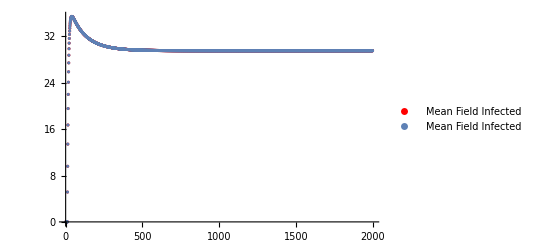

```mathematica
Show[ListPlot[q2[[;;,3]],PlotRange->Full,PlotLegends->{"Mean Field Infected"}, PlotStyle->Red],
ListPlot[q[[;;,3]],PlotRange->Full,PlotLegends->{"Mean Field Infected"}]]
```

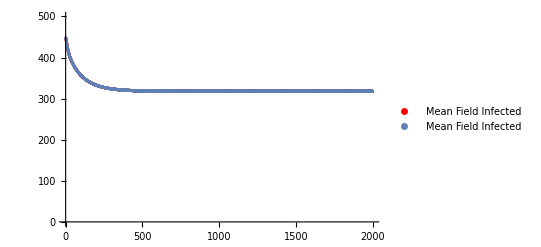

```mathematica
Show[ListPlot[q2[[;;,4]],PlotRange->{0,500},PlotLegends->{"Mean Field Infected"}, PlotStyle->Red],ListPlot[q[[;;,4]],PlotRange->{0,500},PlotLegends->{"Mean Field Infected"}]]
```

## Solve Analytically

```mathematica
Clear[iii,p,f,Q,c,b,λ,nhuman,γ]
eqs ={y==f*Q*c*iii/nhuman*p/(1-p)*(λ/(1-p)-y),
z==peip*y,
iii==b*f*Q/γ*z*(nhuman-iii)/nhuman
}
```

{y==(c f iii p Q (-y+λ/(1-p)))/(nhuman (1-p)),z==peip y,iii==(b f (-iii+nhuman) Q z)/(nhuman γ)}

```mathematica
fp1 =Solve[eqs,{y,z,iii}];
```

```mathematica
fp1/.{p->.9,λ->50,γ->1/200,b->0.55,c->0.15,f->0.3,Q->0.9,peip->0.9^11,nhuman->100}
```

{{y→0,z→0,iii→0},{y→125.702,z→39.4467,iii→92.1357}}

```mathematica
FullSimplify[fp1[[2]]]
```

{y→(nhuman (-1+p)^2 γ-b c f^2 p peip Q^2 λ)/(b f (-1+p) peip Q (1+p (-1+c f Q))),z→(nhuman (-1+p)^2 γ-b c f^2 p peip Q^2 λ)/(b f (-1+p) Q (1+p (-1+c f Q))),iii→(nhuman (-nhuman (-1+p)^2 γ+b c f^2 p peip Q^2 λ))/(c f p Q (nhuman (γ-p γ)+b f peip Q λ))}

```mathematica
(* And so, this gives us an analytical expression for when we expect an equilibrium with nonzero infected mosquitoes and humans *)
R0 =(p λ)/((1-p) nhuman) * (b c (f Q)^2  peip)/(γ (1-p));
R0/.{p->.9,λ->50,γ->1/200,b->0.55,c->0.15,f->0.3,Q->0.9,peip->0.9^11,nhuman->100}
```

16.986

## Comparing to the simulation:

### Ensemble average - compare to results from MACRO-PfSI-alignment_run_2_ensemble.R

```mathematica
(* Initial Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;
Q = 0.9;
p = 0.9; (*surviving mosquitoes*)
EIP = 11; (*days until sporozoite matures*)
γ = 1/200. ; (*rate of end of infectious period*)
λ = 50; (*rate of mosquito emergence*)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt]; Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}];
M  =450;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; (* susceptible individuals *)
```

```mathematica
q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added*)
Mt = p*(M +λ);
(* Step 2: update mosquito infected/infectious counts *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
Zt = p*Z +Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

```mathematica
(* You might need to adjust the file path here *)
simdata = Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/run_2_ensemble/ensemble_average_data.csv"];
```

```mathematica
plota = ListLinePlot[simdata[[;;,1;;2]], PlotStyle->Black,PlotRange->{400,500},  
PlotLegends->{"Simulation Ensemble Mean"},
PlotLabel->"Total Number of Mosquitoes"];
plotb = ListLinePlot[simdata[[;;,2]]+ simdata[[;;,6]], PlotStyle->Red];
plotc = ListLinePlot[simdata[[;;,2]]- simdata[[;;,6]], PlotStyle->Red];
plotd =ListLinePlot[ q[[;;,1]], PlotLegends->{"Mean Field"},PlotStyle->Blue];
Show[plota,plotb, plotc,plotd]
```

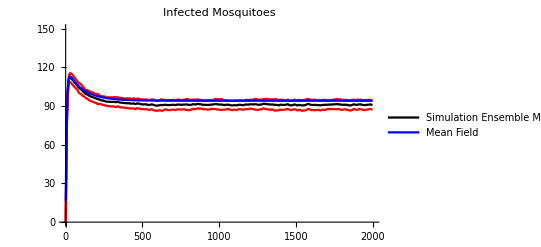

```mathematica
plota = ListLinePlot[simdata[[;;,{1,3}]], PlotStyle->Black,PlotRange->{0,150},  
PlotLegends->{"Simulation Ensemble Mean"},
PlotLabel->"Infected Mosquitoes"];
plotb = ListLinePlot[simdata[[;;,3]]+ simdata[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdata[[;;,3]]- simdata[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotd =ListLinePlot[ q[[;;,2]], PlotLegends->{"Mean Field"},PlotStyle->Blue,PlotRange->Full];
Show[plota,plotb, plotc,plotd]
```

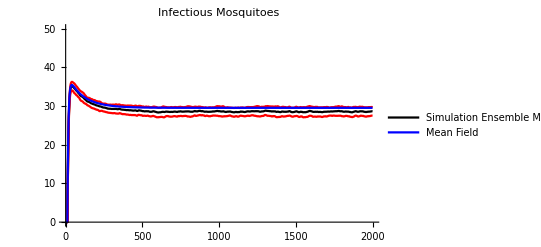

```mathematica
plota = ListLinePlot[simdata[[;;,{1,4}]], PlotStyle->Black,PlotRange->{0,50},  
PlotLegends->{"Simulation Ensemble Mean"},
PlotLabel->"Infectious Mosquitoes"];
plotb = ListLinePlot[simdata[[;;,4]]+ simdata[[;;,8]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdata[[;;,4]]- simdata[[;;,8]], PlotStyle->Red,PlotRange->Full];
plotd =ListLinePlot[ q[[;;,3]], PlotLegends->{"Mean Field"},PlotStyle->Blue,PlotRange->Full];
Show[plota,plotb, plotc,plotd]
```

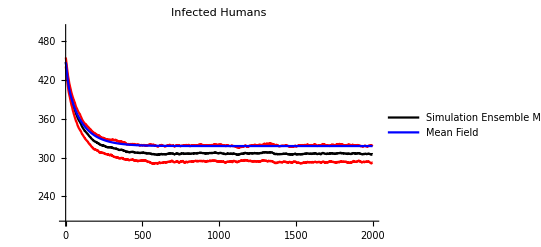

```mathematica
plota = ListLinePlot[simdata[[;;,{1,5}]], PlotStyle->Black,PlotRange->{200,500},  
PlotLegends->{"Simulation Ensemble Mean"},
PlotLabel->"Infected Humans"];
plotb = ListLinePlot[simdata[[;;,5]]+ simdata[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdata[[;;,5]]- simdata[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotd =ListLinePlot[ q[[;;,4]], PlotLegends->{"Mean Field"},PlotStyle->Blue,PlotRange->Full];
Show[plota,plotb, plotc,plotd]
```

### Including the analytical predictions from Ross-Macdonald:

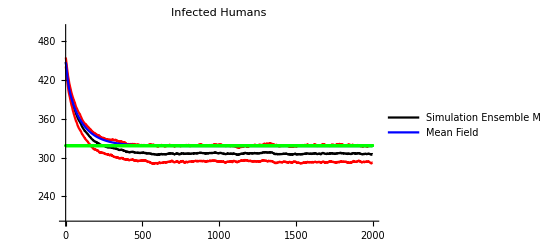

```mathematica
plote = ListPlot[Table[iii/.fp1[[2]]/.peip->.9^11,{x,1,2000}],PlotStyle->Green];
Show[plota,plotb, plotc,plotd,plote]
```

Note how the stochastic simulation is consistently lower than the analytical result - this is a known disagreement, because of O(1) effects which can be quantified exactly using moment closure.

### Ensemble average - compare to results from C++ implementation of MACRO - lambda = 2

Here’s the script for implementing the C++, for comparison with R
https://github.com/smitdave/MASH-Main/blob/master/MASH-dev/SeanWu/MACRO-dev/MACRO-PfSI-ModelValidation.R

```mathematica
(* Initial Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;
Q = 0.9;
p = 0.9; (*surviving mosquitoes*)
EIP = 11; (*days until sporozoite matures*)
γ = 1/200. ; (*rate of end of infectious period*)
λ = 2; (*rate of mosquito emergence*)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt]; Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}];
M  =18;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; 
(* susceptible individuals *) 

q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added*)
Mt = p*(M +λ);
(* Step 2: update mosquito infected/infectious counts *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
Zt = p*Z +Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

```mathematica
(* Importing the data : *)
(*simdataR = Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_R.csv"];
simdataR = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataR[[2;;,;;]]]}]];*)
simdataC = 
Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_2.csv"];

simdataC = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataC[[2;;,;;]]]}]];
```

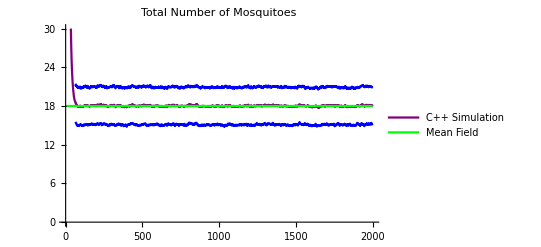

```mathematica
(*plota = ListLinePlot[simdataR[[2;;,1;;2]], PlotStyle->Black,PlotRange->{0,30},  
PlotLegends->{"R Simulation"},
PlotLabel->"Total Number of Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[2;;,1;;2]], PlotStyle->Purple,PlotRange->{0,30},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Total Number of Mosquitoes"];

(*plotb = ListLinePlot[simdataR[[2;;,2]]+ simdataR[[2;;,6]], PlotStyle->Red];
plotc = ListLinePlot[simdataR[[2;;,2]]- simdataR[[2;;,6]], PlotStyle->Red];*)
plotb2 = ListLinePlot[simdataC[[2;;,2]]+ simdataC[[2;;,6]], PlotStyle->Blue];
plotc2 = ListLinePlot[simdataC[[2;;,2]]- simdataC[[2;;,6]], PlotStyle-> Blue];

plotd =ListLinePlot[ q[[;;,1]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

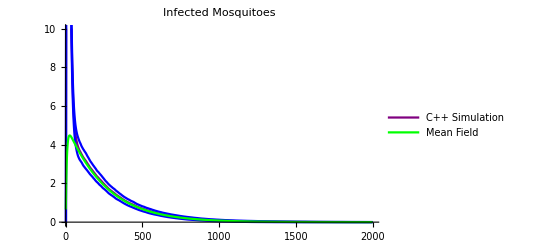

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,3}]], PlotStyle->Black,PlotRange->{60,120},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,3}]], PlotStyle->Purple,PlotRange->{0,10},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Mosquitoes"];
(*plotb = ListLinePlot[simdataR[[;;,3]]+ simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,3]]- simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,3]]+ simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,3]]- simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,2]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

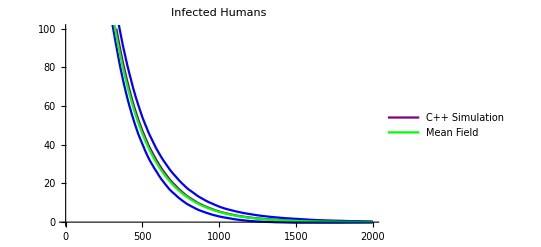

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,5}]], PlotStyle->Black,PlotRange->{250,450},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Humans"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,5}]], PlotStyle->Purple,PlotRange->{0,100},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Humans"];
(*plotb = ListLinePlot[simdataR[[;;,5]]+ simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,5]]- simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,5]]+ simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,5]]- simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,4]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

(*Show[plota,plota2,plotb,plotc,plotb2,plotc2,plotd]*)
Show[plota2,plotb2,plotc2,plotd]
```

### Ensemble average - compare to results from C++ implementation of MACRO - lambda = 5

Here’s the script for implementing the C++, for comparison with R
https://github.com/smitdave/MASH-Main/blob/master/MASH-dev/SeanWu/MACRO-dev/MACRO-PfSI-ModelValidation.R

```mathematica
(* Initial Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;
Q = 0.9;
p = 0.9; (*surviving mosquitoes*)
EIP = 11; (*days until sporozoite matures*)
γ = 1/200. ; (*rate of end of infectious period*)
λ = 5; (*rate of mosquito emergence*)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt]; Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}];
M  =45;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; 
(* susceptible individuals *) 

q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added*)
Mt = p*(M +λ);
(* Step 2: update mosquito infected/infectious counts *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
Zt = p*Z +Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

```mathematica
(* Importing the data : *)
(*simdataR = Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_5.csv"];
simdataR = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataR[[2;;,;;]]]}]];
*)
simdataC = 
Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_5.csv"];

simdataC = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataC[[2;;,;;]]]}]];
```

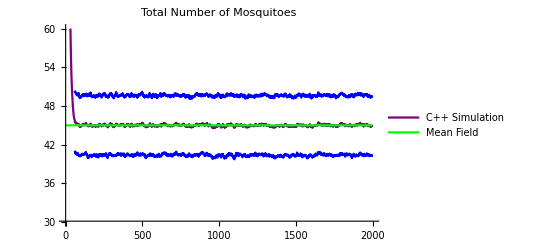

```mathematica
(*plota = ListLinePlot[simdataR[[2;;,1;;2]], PlotStyle->Black,PlotRange->{30,60},  
PlotLegends->{"R Simulation"},
PlotLabel->"Total Number of Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[2;;,1;;2]], PlotStyle->Purple,PlotRange->{30,60},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Total Number of Mosquitoes"];

(*plotb = ListLinePlot[simdataR[[2;;,2]]+ simdataR[[2;;,6]], PlotStyle->Red];
plotc = ListLinePlot[simdataR[[2;;,2]]- simdataR[[2;;,6]], PlotStyle->Red];*)
plotb2 = ListLinePlot[simdataC[[2;;,2]]+ simdataC[[2;;,6]], PlotStyle->Blue];
plotc2 = ListLinePlot[simdataC[[2;;,2]]- simdataC[[2;;,6]], PlotStyle-> Blue];

plotd =ListLinePlot[ q[[;;,1]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

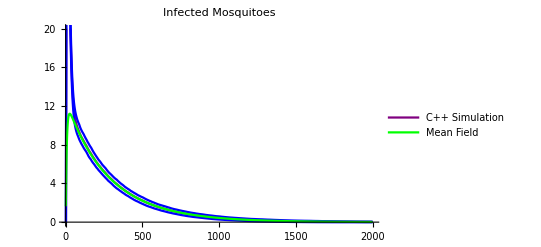

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,3}]], PlotStyle->Black,PlotRange->{60,120},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,3}]], PlotStyle->Purple,PlotRange->{0,20},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Mosquitoes"];
(*plotb = ListLinePlot[simdataR[[;;,3]]+ simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,3]]- simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,3]]+ simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,3]]- simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,2]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

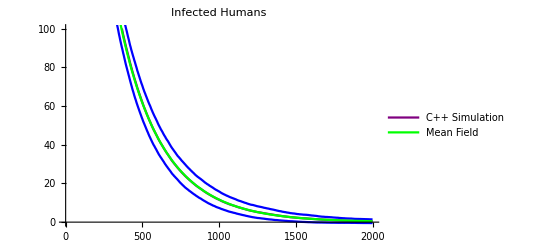

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,5}]], PlotStyle->Black,PlotRange->{250,450},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Humans"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,5}]], PlotStyle->Purple,PlotRange->{0,100},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Humans"];
(*plotb = ListLinePlot[simdataR[[;;,5]]+ simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,5]]- simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,5]]+ simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,5]]- simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,4]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

### Ensemble average - compare to results from C++ implementation of MACRO - lambda = 10

Here’s the script for implementing the C++, for comparison with R
https://github.com/smitdave/MASH-Main/blob/master/MASH-dev/SeanWu/MACRO-dev/MACRO-PfSI-ModelValidation.R

```mathematica
(* Initial Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;
Q = 0.9;
p = 0.9; (*surviving mosquitoes*)
EIP = 11; (*days until sporozoite matures*)
γ = 1/200. ; (*rate of end of infectious period*)
λ = 10; (*rate of mosquito emergence*)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt]; Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}];
M  =90;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; 
(* susceptible individuals *) 

q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added*)
Mt = p*(M +λ);
(* Step 2: update mosquito infected/infectious counts *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
Zt = p*Z +Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

```mathematica
(* Importing the data : *)
(*simdataR = Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_5.csv"];
simdataR = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataR[[2;;,;;]]]}]];
*)
simdataC = 
Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_10.csv"];

simdataC = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataC[[2;;,;;]]]}]];
```

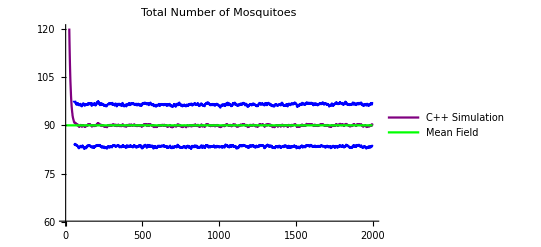

```mathematica
(*plota = ListLinePlot[simdataR[[2;;,1;;2]], PlotStyle->Black,PlotRange->{30,60},  
PlotLegends->{"R Simulation"},
PlotLabel->"Total Number of Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[2;;,1;;2]], PlotStyle->Purple,PlotRange->{60,120},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Total Number of Mosquitoes"];

(*plotb = ListLinePlot[simdataR[[2;;,2]]+ simdataR[[2;;,6]], PlotStyle->Red];
plotc = ListLinePlot[simdataR[[2;;,2]]- simdataR[[2;;,6]], PlotStyle->Red];*)
plotb2 = ListLinePlot[simdataC[[2;;,2]]+ simdataC[[2;;,6]], PlotStyle->Blue];
plotc2 = ListLinePlot[simdataC[[2;;,2]]- simdataC[[2;;,6]], PlotStyle-> Blue];

plotd =ListLinePlot[ q[[;;,1]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

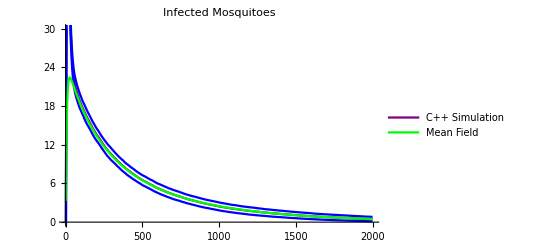

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,3}]], PlotStyle->Black,PlotRange->{60,120},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,3}]], PlotStyle->Purple,PlotRange->{0,30},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Mosquitoes"];
(*plotb = ListLinePlot[simdataR[[;;,3]]+ simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,3]]- simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,3]]+ simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,3]]- simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,2]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

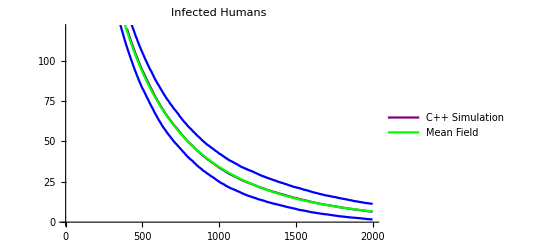

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,5}]], PlotStyle->Black,PlotRange->{250,450},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Humans"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,5}]], PlotStyle->Purple,PlotRange->{0,120},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Humans"];
(*plotb = ListLinePlot[simdataR[[;;,5]]+ simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,5]]- simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,5]]+ simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,5]]- simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,4]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

### Ensemble average - compare to results from C++ implementation of MACRO - lambda = 20

Here’s the script for implementing the C++, for comparison with R
https://github.com/smitdave/MASH-Main/blob/master/MASH-dev/SeanWu/MACRO-dev/MACRO-PfSI-ModelValidation.R

```mathematica
(* Initial Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;
Q = 0.9;
p = 0.9; (*surviving mosquitoes*)
EIP = 11; (*days until sporozoite matures*)
γ = 1/200. ; (*rate of end of infectious period*)
λ = 20; (*rate of mosquito emergence*)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt]; Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}];
M  =180;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; 
(* susceptible individuals *) 

q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added*)
Mt = p*(M +λ);
(* Step 2: update mosquito infected/infectious counts *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
Zt = p*Z +Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

```mathematica
(* Importing the data : *)
(*simdataR = Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_5.csv"];
simdataR = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataR[[2;;,;;]]]}]];
*)
simdataC = 
Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_20.csv"];

simdataC = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataC[[2;;,;;]]]}]];
```

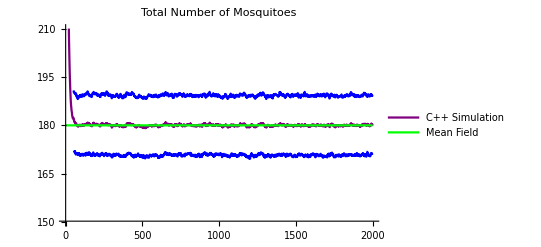

```mathematica
(*plota = ListLinePlot[simdataR[[2;;,1;;2]], PlotStyle->Black,PlotRange->{30,60},  
PlotLegends->{"R Simulation"},
PlotLabel->"Total Number of Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[2;;,1;;2]], PlotStyle->Purple,PlotRange->{150,210},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Total Number of Mosquitoes"];

(*plotb = ListLinePlot[simdataR[[2;;,2]]+ simdataR[[2;;,6]], PlotStyle->Red];
plotc = ListLinePlot[simdataR[[2;;,2]]- simdataR[[2;;,6]], PlotStyle->Red];*)
plotb2 = ListLinePlot[simdataC[[2;;,2]]+ simdataC[[2;;,6]], PlotStyle->Blue];
plotc2 = ListLinePlot[simdataC[[2;;,2]]- simdataC[[2;;,6]], PlotStyle-> Blue];

plotd =ListLinePlot[ q[[;;,1]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

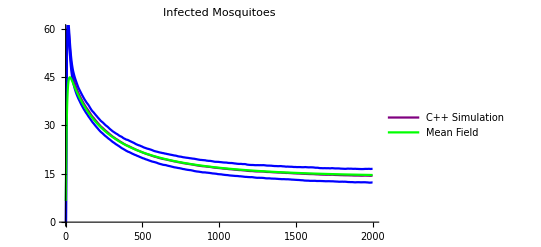

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,3}]], PlotStyle->Black,PlotRange->{60,120},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,3}]], PlotStyle->Purple,PlotRange->{0,60},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Mosquitoes"];
(*plotb = ListLinePlot[simdataR[[;;,3]]+ simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,3]]- simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,3]]+ simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,3]]- simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,2]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

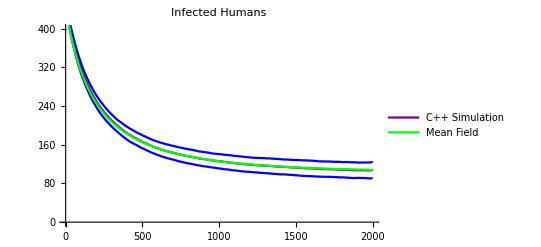

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,5}]], PlotStyle->Black,PlotRange->{250,450},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Humans"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,5}]], PlotStyle->Purple,PlotRange->{0,400},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Humans"];
(*plotb = ListLinePlot[simdataR[[;;,5]]+ simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,5]]- simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,5]]+ simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,5]]- simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,4]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

### Ensemble average - compare to results from C++ implementation of MACRO - lambda = 50 (includes R comparison)

Here’s the script for implementing the C++, for comparison with R
https://github.com/smitdave/MASH-Main/blob/master/MASH-dev/SeanWu/MACRO-dev/MACRO-PfSI-ModelValidation.R

```mathematica
(* Initial Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;
Q = 0.9;
p = 0.9; (*surviving mosquitoes*)
EIP = 11; (*days until sporozoite matures*)
γ = 1/200. ; (*rate of end of infectious period*)
λ = 50; (*rate of mosquito emergence*)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt]; Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}];
M  =450;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; 
(* susceptible individuals *) 

q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added*)
Mt = p*(M +λ);
(* Step 2: update mosquito infected/infectious counts *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
Zt = p*Z +Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

```mathematica
(* Importing the data : *)
simdataR = Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_R_lambda50.csv"];
simdataC = 
Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_CPP_lambda50.csv"];
simdataR = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataR[[2;;,;;]]]}]];
simdataC = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataC[[2;;,;;]]]}]];
```

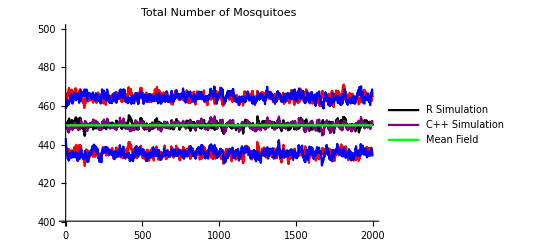

```mathematica
plota = ListLinePlot[simdataR[[2;;,1;;2]], PlotStyle->Black,PlotRange->{400,500},  
PlotLegends->{"R Simulation"},
PlotLabel->"Total Number of Mosquitoes"];
plota2 = ListLinePlot[simdataC[[2;;,1;;2]], PlotStyle->Purple,PlotRange->{400,500},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Total Number of Mosquitoes"];

plotb = ListLinePlot[simdataR[[2;;,2]]+ simdataR[[2;;,6]], PlotStyle->Red];
plotc = ListLinePlot[simdataR[[2;;,2]]- simdataR[[2;;,6]], PlotStyle->Red];
plotb2 = ListLinePlot[simdataC[[2;;,2]]+ simdataC[[2;;,6]], PlotStyle->Blue];
plotc2 = ListLinePlot[simdataC[[2;;,2]]- simdataC[[2;;,6]], PlotStyle-> Blue];

plotd =ListLinePlot[ q[[;;,1]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota,plota2,plotb,plotc,plotb2,plotc2,plotd]
```

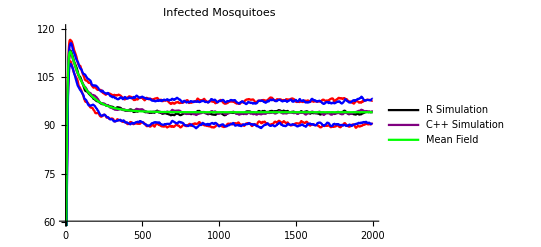

```mathematica
plota = ListLinePlot[simdataR[[;;,{1,3}]], PlotStyle->Black,PlotRange->{60,120},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Mosquitoes"];
plota2 = ListLinePlot[simdataC[[;;,{1,3}]], PlotStyle->Purple,PlotRange->{60,120},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Mosquitoes"];
plotb = ListLinePlot[simdataR[[;;,3]]+ simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,3]]- simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotb2 = ListLinePlot[simdataC[[;;,3]]+ simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,3]]- simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,2]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota,plota2,plotb,plotc,plotb2,plotc2,plotd]
```

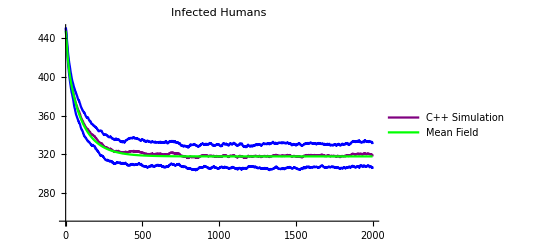

```mathematica
plota = ListLinePlot[simdataR[[;;,{1,5}]], PlotStyle->Black,PlotRange->{250,450},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Humans"];
plota2 = ListLinePlot[simdataC[[;;,{1,5}]], PlotStyle->Purple,PlotRange->{250,450},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Humans"];
plotb = ListLinePlot[simdataR[[;;,5]]+ simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,5]]- simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotb2 = ListLinePlot[simdataC[[;;,5]]+ simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,5]]- simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,4]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

(*Show[plota,plota2,plotb,plotc,plotb2,plotc2,plotd]*)
Show[plota2,plotb2,plotc2,plotd]
```

### Ensemble average - compare to results from C++ implementation of MACRO - lambda = 100

Here’s the script for implementing the C++, for comparison with R
https://github.com/smitdave/MASH-Main/blob/master/MASH-dev/SeanWu/MACRO-dev/MACRO-PfSI-ModelValidation.R

```mathematica
(* Initial Parameters *)
nhuman = 500; (*total number of people*)
b = 0.55; (*fraction of bites on infectious humans infect a mosquito*)
c = 0.15; (*fraction of infectious bites infect a human*)
f = 0.3;
Q = 0.9;
p = 0.9; (*surviving mosquitoes*)
EIP = 11; (*days until sporozoite matures*)
γ = 1/200. ; (*rate of end of infectious period*)
λ = 100; (*rate of mosquito emergence*)
PfPR = .9; (* parasite rate, sets initial number of infected individuals *)
(*Number of Time Steps*)
tsteps =2000;
(*Initialize State Variables*)
Clear[M,Y,Z,Mt,Yt,Zt]; Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}];
M  =900;(*total adult mosquitoes*)
Y = 0; (*total infected adult mosquitoes*)
Z =0; (*total infectious adult mosquitoes*)
Do[Subscript[ZZ, i]=0,{i,1,EIP}]; Do[Subscript[ZZt, i]=0,{i,1,EIP}]; (* Store the number infected at t-EIP up through the present t*) 
ii = nhuman*PfPR; (* infected individuals *)
s = nhuman - ii; 
(* susceptible individuals *) 

q = Table[
(* Step 1: Patch Dynamics dictate how many new adults are added*)
Mt = p*(M +λ);
(* Step 2: update mosquito infected/infectious counts *)
Yt = p*Y +f*Q*c*ii/nhuman*p* (M + λ -Y);
Zt = p*Z +Subscript[ZZ, 1];
Do[Subscript[ZZt, i]=Subscript[ZZ, i+1],{i,1,EIP-1}];
Subscript[ZZt, EIP]=p^EIP*f*Q*c*ii/nhuman*p*(M+ λ  - Y);
(* Step 3: update humans *)
iit= ii - γ * ii +(1-Exp[- b*f*Q*Z/nhuman])(nhuman - ii);
(* Update state variables and output *)
M = Mt;
Y = Yt;
Z = Zt;
Do[Subscript[ZZ, i]=Subscript[ZZt, i],{i,1,EIP}];
ii = iit;
{M, Y, Z, ii},
{i,1,tsteps}];
```

```mathematica
(* Importing the data : *)
(*simdataR = Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_5.csv"];
simdataR = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataR[[2;;,;;]]]}]];
*)
simdataC = 
Import["/Users/dtcitron/Documents/MASH/MASH-Main/MASH-dev/DanielCitron/MACRO-model-alignment/cpp-r-ensemble-comparisons/ensemble_average_data_100.csv"];

simdataC = Transpose[Catenate[{{Table[i,{i,1,2000}]},Transpose[simdataC[[2;;,;;]]]}]];
```

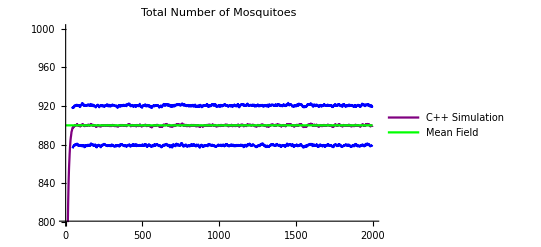

```mathematica
(*plota = ListLinePlot[simdataR[[2;;,1;;2]], PlotStyle->Black,PlotRange->{30,60},  
PlotLegends->{"R Simulation"},
PlotLabel->"Total Number of Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[2;;,1;;2]], PlotStyle->Purple,PlotRange->{800,1000},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Total Number of Mosquitoes"];

(*plotb = ListLinePlot[simdataR[[2;;,2]]+ simdataR[[2;;,6]], PlotStyle->Red];
plotc = ListLinePlot[simdataR[[2;;,2]]- simdataR[[2;;,6]], PlotStyle->Red];*)
plotb2 = ListLinePlot[simdataC[[2;;,2]]+ simdataC[[2;;,6]], PlotStyle->Blue];
plotc2 = ListLinePlot[simdataC[[2;;,2]]- simdataC[[2;;,6]], PlotStyle-> Blue];

plotd =ListLinePlot[ q[[;;,1]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

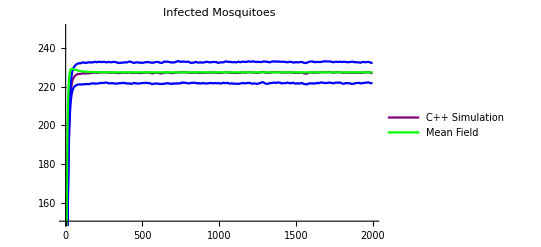

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,3}]], PlotStyle->Black,PlotRange->{60,120},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Mosquitoes"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,3}]], PlotStyle->Purple,PlotRange->{150,250},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Mosquitoes"];
(*plotb = ListLinePlot[simdataR[[;;,3]]+ simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,3]]- simdataR[[;;,7]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,3]]+ simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,3]]- simdataC[[;;,7]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,2]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```

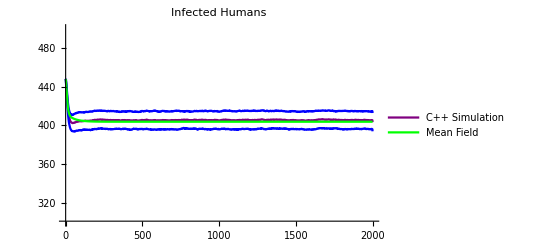

```mathematica
(*plota = ListLinePlot[simdataR[[;;,{1,5}]], PlotStyle->Black,PlotRange->{250,450},  
PlotLegends->{"R Simulation"},
PlotLabel->"Infected Humans"];*)
plota2 = ListLinePlot[simdataC[[;;,{1,5}]], PlotStyle->Purple,PlotRange->{300,500},  
PlotLegends->{"C++ Simulation"},
PlotLabel->"Infected Humans"];
(*plotb = ListLinePlot[simdataR[[;;,5]]+ simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];
plotc = ListLinePlot[simdataR[[;;,5]]- simdataR[[;;,9]], PlotStyle->Red,PlotRange->Full];*)
plotb2 = ListLinePlot[simdataC[[;;,5]]+ simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];
plotc2 = ListLinePlot[simdataC[[;;,5]]- simdataC[[;;,9]], PlotStyle->Blue,PlotRange->Full];

plotd =ListLinePlot[ q[[;;,4]], PlotLegends->{"Mean Field"},PlotStyle->Green,PlotRange->Full];

Show[plota2,plotb2,plotc2,plotd]
```